# The Multiparadigm Data Science Workflow

## Analyze and Communicate

## -Graphics-

*Slide Credits to Abrita of WolframU, Data Science Bootcamp Summer 2020

## Stage 4: Analyze

## Quick Review of Terms

Terminology borrowed from both statistics and machine learning:

Independent variables

Or predictor variables or features

x⃗=={x_1 …,x_n}

Dependent variable

Or response variable or label or output

y

Model

A function and associated optimization criteria (e.g. distributional assumptions) used to approximate the behavior suggested by the data

y==f(x⃗)

A blackbox represented by an algorithm that takes training data as input and produces labels/predictions as output

x⃗→Blackbox→y

Parameters

The values in the model or algorithm that are not assumed by the predictor or response variables; learned/tuned while training

Training

The process of identifying the function or the algorithm (and the corresponding parameters) that best represents the relationship between the input and output

## Is This A or B (or C or D or E…)?

### Class 1 or Class 2?

Cat or dog:

```mathematica
ImageIdentify[{-Graphics-,-Graphics-}]
```

Spam or not:

```mathematica
Classify["Spam", {"SALE! SALE! SALE!","Lunch on Monday?"}]
```

English, French, Spanish, Arabic or another language:

```mathematica
Classify["Language", {"the house is blue", "la maison est bleue", "la casa es azul",  "المنزل باللون الأزرق","das Haus ist blau", "房子是蓝色的", "будинок синій"}]
```

Facebook post on technology, food or travel:

```mathematica
Classify["FacebookTopic", {"I bought a new computer", "Soup and salad for lunch", "I'm going to Paris"}]
```

## Classification

Supervised learning task: predict the class label of a sample, based on previously labeled instances:

{Age, Income} Features→High/Low (Credit Risk) Label

Training data is usually a list of labeled samples:

Feature1 | Feature2 | Label
Age | Income | Credit Risk
38 | 85786 | No
55 | 70115 | No
71 | 55299 | Yes
49 | 41035 | No
50 | 59230 | Yes

The goal of classification is to:

Infer a function from the data, mapping from feature values to label

Given a new data point, use this function to return a label based on the feature values:

{35,65000}Sample Features→NoPredicted Label

## Machine Learning Superfunction: Classify

Classify can be used on many types of data, including numerical, textual, sounds and images, as well as combinations of these.

Train a classifier to label images as “dog” or “cat”:

```mathematica
dogCatClassifier =Classify[<|"cat"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},"dog"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>]
```

Test the classifier on new images:

```mathematica
dogCatClassifier[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

Train a classifier to provide image labels for text data:

```mathematica
dogCatClassifier2=Classify[{"the cat is grey"->-Graphics-,"my cat is fast"->-Graphics-,"this dog is scary"->-Graphics- ,"the big dog"->-Graphics-}]
```

Test the classifier on new text:

```mathematica
dogCatClassifier2[{"nice cat","what a dog"}]
```

## What Can Classify Provide?

Obtain a ClassifierFunction for the training data:

```mathematica
c=Classify[{
{1.5,Blue}->"A",
{3.2,Blue}->"A",
{4.1,Red}->"B",
{5.3,Red}->"B",
{10.,Green}->"C",
{12.4,Red}->"C"}]
```

#### Decision

By default, ClassifierFunction provides a decision about the class label:

```mathematica
c[{10.1,Blue}]
```

#### Probabilities for all possible classes

ClassifierFunction can also provide the probabilities of the sample belonging to each class:

```mathematica
c[{10.1,Blue},"Probabilities"]
```

#### Probability for a specific class

ClassifierFunction can also provide the probability of the sample belonging to a particular class:

```mathematica
c[{10.1,Blue},"Probability"->"A"]
```

Probability of the sample belonging to class "A", as the value of feature 1 changes while feature 2 remains the same:

```mathematica
Plot[c[{x,Blue},"Probability"->"A"],{x,0,15},Exclusions->None,PlotRange->{Automatic,{0,1}}]
```

## Classify Mythical Creatures

Learn to identify mythical creatures using a set of pre-labeled inputs:

```mathematica
legendary =Classify[<|"Griffin"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},"Centaur"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},"Dragon"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},"Unicorn"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>]
```

Try to identify the mythical creature in the new inputs:

```mathematica
legendary[{-Graphics-, -Graphics-, -Graphics-, -Graphics-}]
```

## Customizing Classify: Method

This is for your own information of what Mathematica has to offer. Fun to know do not have to use all of them.

Classify can be configured to use one of many well-known classification algorithms as a Method:

LogisticRegression to classify using probabilities from linear combinations of features

NearestNeighbors to classify from nearest-neighbor examples

NaiveBayes to classify by assuming probabilistic independence of features

DecisionTree to classify using a tree-like model for representing decisions and their consequences

GradientBoostedTrees to classify using an ensemble of trees trained with gradient boosting

RandomForest to classify using Breiman–Cutler ensembles of decision trees

Markov Model to classify using a stochastic model on the sequence of features (for text, bag of tokens, etc.)

SupportVectorMachine to classify using a disciminative model that constructs a hyperplane or sets of hyperplanes to separate samples of different classes

NeuralNetwork to classify using algorithms modeled loosely after biological neural networks

## Compare the Performance of Two Classifiers

Set up the training data:

```mathematica
trainingset = {1,2,3,4,5,6,7}-> {"a","a", "b", "a", "b","b","b"};
```

Build a classifier using LogisticRegression:

```mathematica
logistic=Classify[trainingset, Method->"LogisticRegression"]
```

Build a classifier using NaiveBayes:

```mathematica
naiveb=Classify[trainingset, Method->"NaiveBayes"]
```

Use both classifiers to generate the probability for a specific output label for a range of inputs:

```mathematica
Plot[{
logistic[x,"Probability"->"a"],
naiveb[x,"Probability"->"a"]
}, {x,0,8}, Exclusions->None,PlotLegends->{"Logistic Regression","Naive Bayes"}]
```

## Customizing Classify

Classify can be customized with the following:

TheIndeterminateThresholdoption can be used to specify the class probabilities for which the ClassifierFunction should provide a decision.

The UtilityFunction option can be used to specify how a ClassifierFunction makes decisions.

A classifier’s performance can be optimized for training speed, actual runtime speed, memory usage or accuracy of predictions, with the PerformanceGoal option.

These are not required for your homework but can be fun to play around with!

## How Much or How Many?

### Questions for Classification

Is this A or B?

Class 1 or class 2…

Healthy tissue or cancerous…

High risk or low risk…

### Questions for Regression

How much or how many?

Price of a home…

Runs scored by a baseball player…

Yield of a power plant…

## Regression

Classification:

{Age,Income}Features→Credit Risk (High/Low)Label

Regression:

{Age,Income}Features→Credit ScoreTarget

Sample dataset:

Age | Income | Credit Score
25 | 20304 | 423
58 | 87813 | 745
20 | 28000 | 515
40 | 60598 | 640
64 | 70603 | 710

Set up the sample data:

```mathematica
data =
{{25,20304,423},
{58,87813,745},
{20,28000,515},
{40,60598,640},
{64,70603,710}}
```

Linear regression:

```mathematica
lm=LinearModelFit[data,{x,y},{x,y}]
```

```mathematica
lm["BestFit"]
```

Use best fit to compute the credit score for a given age and income:

```mathematica
lm["BestFit"]/.{x->35,y->65000}
```

Fit for income = 50,000:

```mathematica
Show[ListPlot[data[[All,{1,3}]],PlotStyle->Red],Plot[lm["BestFit"]/. y-> 50000,{x,20,60}]]
```

## Machine Learning Superfunction: Predict

Predict can be used on many types of data, including numerical, textual, sounds and images, as well as combinations of these.

Set up the training data:

```mathematica
d=Dataset[{
<|"age"->32,"height"->160, "gender"-> "female"|>,
<|"height"->183,"age"->41,"gender"-> "female"|>,
<|"height"->123,"age"->30,"gender"-> "female"|>,
<|"height"->175,"age"->21,"gender"-> "male"|>,
<|"height"->150,"age"->11,"gender"-> "male"|>,
<|"age"->52,"height"->164,"gender"-> "female"|>}];
```

Train a PredictorFunction to predict age from gender and height:

```mathematica
p=Predict[d->"age"]
```

Predict the age for a sample with height = 120 and gender = “female”:

```mathematica
p[{120,"female"}]
```

Predict the age for a sample with height = 150 and gender = “male”:

```mathematica
p[{150,"male"}]
```

Import a dataset of images of gauge readings and divide into training and test sets:

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"data"}]];
Get["gauges.mx"];
trainingGauges =gaugeData[[;;95]];
testGauges = gaugeData[[96;;]];
```

Look at some random samples from the training set:

```mathematica
Grid[Partition[RandomSample[trainingGauges,9],3]]
```

Train a PredictorFunction to predict the values of the gauge readings from the images:

```mathematica
predictor=Predict[trainingGauges,Method->"NearestNeighbors"]
```

Test gauge image:

-Graphics-

Predict a value for the test image:

```mathematica
predictor[-Graphics-]
```

Predict the values for a list of test images:

```mathematica
predictor[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

Predict a distribution of values conditioned on the input:

```mathematica
predictor[-Graphics-,"Distribution"]
```

Plot the PDF of the distribution:

```mathematica
Plot[PDF[predictor[-Graphics-,"Distribution"],x],{x,0,1}]
```

## Predicting Home Price

Description of the "BostonHomes" dataset in ExampleData:

```mathematica
ExampleData[{"MachineLearning","BostonHomes"},"Description"]
```

Description of the features in the "BostonHomes" data:

```mathematica
ExampleData[{"MachineLearning","BostonHomes"},"VariableDescriptions"]
```

Train a PredictorFunction on the training samples:

```mathematica
p=Predict[ExampleData[{"MachineLearning","BostonHomes"},"TrainingData"],PerformanceGoal->"Quality"]
```

Look at a few random test samples:

```mathematica
RandomSample[ExampleData[{"MachineLearning","BostonHomes"},"TestData"],5]
```

Evaluate the performance of the PredictorFunction using the test data:

```mathematica
pm=PredictorMeasurements[p,ExampleData[{"MachineLearning","BostonHomes"},"TestData"]]
```

Obtain a comparison of the predicted versus actual values:

```mathematica
pm["ComparisonPlot"]
```

Report the standard deviation for the predicted values:

```mathematica
pm["StandardDeviation"]
```

Obtain a full report of the predictor’s performance:

```mathematica
pm["Report"]
```

## Customizing Predict

### Method

The Predict function can be customized to use a specific algorithm by setting the Method option:

LinearRegression

NearestNeighbors

DecisionTree

GradientBoostedTrees

NeuralNetwork

RandomForest

GaussianProcess

This is more for your knowledge and exploration. We are giving you the tools that can be further built upon!

## Unsupervised Learning

Questions that can be answered by supervised machine learning:

Classification

Is this A or B? (Is this A or B or C or D…?)

Regression

How many or how much?

Questions that can be answered by unsupervised machine learning:

How is the data organized?

Does the data have some inherent structure?

Do the samples sort themselves out into different groups and subgroups?

## Cluster Analysis

```mathematica
img = -Graphics-;
CellPrint[ExpressionCell[Manipulate[With[{axislabels = ExampleData[{"MachineLearning","FisherIris"},"VariableDescriptions"][[1]],
data = ExampleData[{"MachineLearning","FisherIris"},"Data"]},ListPlot[FindClusters[data[[All,1,{x,y}]],n, Method->"KMeans"],PlotMarkers->Automatic,AspectRatio -> 1,Axes->False,Frame-> {{True,False},{True,False}},FrameTicks -> Automatic,FrameLabel->{{axislabels[[y]],None},{axislabels[[x]],None}},FrameTicks->None]],
Style[Image[ img,ImageSize->Small]],
Style["Three species of Iris flower:\nSetosa, Versicolor, Virginica", "Text"],
"",
Delimiter,
"",
Style["Features", 12, Bold],
"",
{{x,1,"Feature 1 (x axis)"},{1->"Sepal Length",2->"Sepal Width",3->"Petal Length",4->"Petal Width"}},
{{y,2,"Feature 2 (y axis)"},{1->"Sepal Length",2->"Sepal Width",3->"Petal Length",4->"Petal Width"}},
"",
Delimiter,
Style["Number of Clusters", 12, Bold],
{{n,2,"k"},1,5,1,ControlType->Setter},
ControlType->PopupMenu,
ControlPlacement->Left,FrameLabel->{{None,None},{None,Style["Fisher's Iris Data: K-Means Clustering",18]}},SynchronousUpdating->False,SaveDefinitions->True],"Output",GeneratedCell->False]]
```

## FindClusters

Use FindClusters to cluster a list of positive and negative integers:

```mathematica
FindClusters[{-7,-7,-5,-5,-10,-10,-5,-10,-9,-8,-10,-9,-8,-7,5,6,7,8,5,10,3,10,5,4,4,2,3,4}]
```

The number of clusters can be explicitly specified:

```mathematica
images={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
FindClusters[images,3]
```

## Clustering Algorithms

Different clustering algorithms can be specified using the Method option:

```mathematica
FindClusters[data,Method->"DBSCAN"]
```

{{0.841471,0.909297,0.14112,-0.756802,-0.958924,-0.279415,0.656987,0.989358,0.412118,-0.544021}}

Create a synthetic dataset:

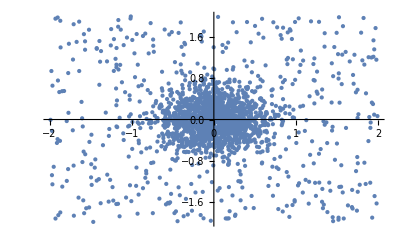

```mathematica
SeedRandom[2];
data1 = RandomVariate[MultinormalDistribution[{0,0},{{.1,0},{0,.1}}],1500];
data2 = RandomVariate[UniformDistribution[{{-2,2}, {-2,2}}],500];
test = Join[data1,data2];
ListPlot[test,PlotStyle->PointSize[Medium]]
```

Use the k-means algorithm for clustering:

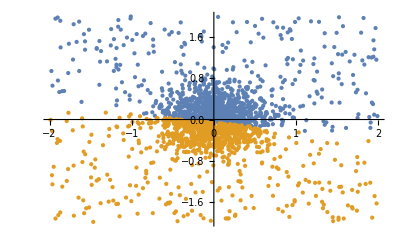

```mathematica
ListPlot[FindClusters[test,2,Method->"KMeans"],PlotStyle->PointSize[Medium]]
```

Use the DBSCAN algorithm for clustering:

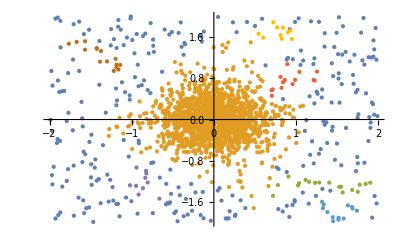

```mathematica
ListPlot[FindClusters[test,Method->"DBSCAN"],PlotStyle->PointSize[Medium]]
```

## Other Ways to Find Clusters

A list of colors:

```mathematica
colors = RandomColor[30]
```

{RGBColor[0.42880669394347026, 0.6313263749218327, 0.04017197523732796],RGBColor[0.5322844567602745, 0.20934524063040416, 0.4625304315913801],RGBColor[0.1216024506457376, 0.9259363652997707, 0.7560869383761055],RGBColor[0.5370012775490045, 0.6769216710609116, 0.010526530822881242],RGBColor[0.8614617783949217, 0.7459514645065781, 0.522653181119024],RGBColor[0.4896967720344436, 0.9691422592169678, 0.7118387212463448],RGBColor[0.9081392039259952, 0.13651539486568853, 0.7420036662522862],RGBColor[0.9921331973646756, 0.45862022554859516, 0.5922318171482548],RGBColor[0.04937458577673093, 0.41734508919177715, 0.21098380833470554],RGBColor[0.2062322825901335, 0.25754211034864105, 0.7661189387600418],RGBColor[0.6932470433510147, 0.4401657069396381, 0.978662712158674],RGBColor[0.6448783012102666, 0.5036808006397588, 0.017099857793755113],RGBColor[0.5245801105298751, 0.1788358267934027, 0.30155360286361743],RGBColor[0.8945685988059731, 0.4035929890094343, 0.04704565152941487],RGBColor[0.26211417290451333, 0.6403715671807986, 0.8549799894437393],RGBColor[0.8995137310201922, 0.8106098881046664, 0.7404162493611282],RGBColor[0.24537284677038218, 0.9550392767284799, 0.7449269427153833],RGBColor[0.7253565751873425, 0.6562957841435455, 0.2938937613517303],RGBColor[0.8307635507963509, 0.7730250025889249, 0.10357489678836473],RGBColor[0.7751431736716752, 0.11962603565080987, 0.7604249690550002],RGBColor[0.9760011504311707, 0.42411390523039016, 0.5711718606945924],RGBColor[0.5052094526238524, 0.058709816169977946, 0.9751608167326571],RGBColor[0.0734088422797694, 0.5296238959126476, 0.04428185023975262],RGBColor[0.5326041643350432, 0.6981088213370117, 0.4769251772272436],RGBColor[0.7992215969205407, 0.42737139553088066, 0.6752697021860832],RGBColor[0.7627986832946148, 0.45616796872766496, 0.5821840426452396],RGBColor[0.8258027801385157, 0.35916809045062004, 0.9935613732820141],RGBColor[0.7402777334420556, 0.3558994583717976, 0.897170114623848],RGBColor[0.8575046726708695, 0.5376520318193585, 0.10576367576615575],RGBColor[0.0229704286049639, 0.06727965634325117, 0.8166447182490686]}

Use a ClusteringTree to visualize the clusters in the data:

```mathematica
ClusteringTree[colors,ClusterDissimilarityFunction->"Centroid"]
```

Use a Dendrogram to visualize and understand the distance between the clusters in the data:

```mathematica
Dendrogram[colors,ClusterDissimilarityFunction->"Centroid"]
```

Use ClusteringComponents to get the indices of the clusters to which each sample belongs:

```mathematica
ClusteringComponents[{10,4,5,6,11},2]
```

Use Nearest to find the elements closest to a given sample:

```mathematica
Nearest[{1,2,10,12,3,1,13,25},8]
```

Find the five nearest data points to a given sample:

```mathematica
Nearest[{1,2,10,12,3,1,13,25},8,5]
```

A dataset of mythical creature images:

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"data","creatures.mx"}]]
```

```mathematica
(RandomSample[#1,2]&)/@creatures
```

Use FeatureNearest to create a function to find similar or nearest samples:

```mathematica
nf=FeatureNearest[Flatten[Values[creatures]]]
```

Use it on some test images:

```mathematica
nf[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

Use FeatureSpacePlot on images:

```mathematica
FeatureSpacePlot[EntityClass["Country","Asia"][EntityProperty["Country","Flag"]]]
```

Use FeatureSpacePlot on audio:

```mathematica
list=ExampleData/@ExampleData["Audio"];FeatureSpacePlot[list,LabelingFunction->Callout]
```

Use FeatureSpacePlot on text:

```mathematica
animals={"Alligator","Ant","Bear","Bee","Bird","Camel","Cat","Cheetah","Chicken","Chimpanzee","Cow","Crocodile","Deer","Dog","Dolphin","Duck","Eagle","Elephant","Fish","Fly"};fruits={"Apple","Apricot","Avocado","Banana","Blackberry","Blueberry","Cherry","Coconut","Cranberry","Grape","Turnip","Mango","Melon","Papaya","Peach","Pineapple","Raspberry","Strawberry","Ribes","Fig"};FeatureSpacePlot[Join[animals,fruits],FeatureExtractor->NetModel["GloVe 300-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"]]
```

## Classification with Clustering

ClusterClassify can create a ClassifierFunction directly from the clustering of unlabeled data.

Labeled data:

-10 | Class A
-9 | Class A
-8 | Class A
-7 | Class A
5 | Class B
6 | Class B
7 | Class B
8 | Class B

Clustered unlabeled data:

{-10,-9,-8,-7}
{5,6,7,8}

Build a classifier from the clustering:

```mathematica
c=ClusterClassify[{-10,-9,-8,-7,5,6,7,8}]
```

```mathematica
c/@{-10,-9,-8,-7,5,6,7,8}
```

Classify new data points:

```mathematica
c[-4]
```

```mathematica
c[10]
```

Cluster the colors into three groups and then classify a new color:

{RGBColor[0.42880669394347026, 0.6313263749218327, 0.04017197523732796],RGBColor[0.5322844567602745, 0.20934524063040416, 0.4625304315913801],RGBColor[0.1216024506457376, 0.9259363652997707, 0.7560869383761055],RGBColor[0.5370012775490045, 0.6769216710609116, 0.010526530822881242],RGBColor[0.8614617783949217, 0.7459514645065781, 0.522653181119024],RGBColor[0.4896967720344436, 0.9691422592169678, 0.7118387212463448],RGBColor[0.9081392039259952, 0.13651539486568853, 0.7420036662522862],RGBColor[0.9921331973646756, 0.45862022554859516, 0.5922318171482548],RGBColor[0.04937458577673093, 0.41734508919177715, 0.21098380833470554],RGBColor[0.2062322825901335, 0.25754211034864105, 0.7661189387600418],RGBColor[0.6932470433510147, 0.4401657069396381, 0.978662712158674],RGBColor[0.6448783012102666, 0.5036808006397588, 0.017099857793755113],RGBColor[0.5245801105298751, 0.1788358267934027, 0.30155360286361743],RGBColor[0.8945685988059731, 0.4035929890094343, 0.04704565152941487],RGBColor[0.26211417290451333, 0.6403715671807986, 0.8549799894437393],RGBColor[0.8995137310201922, 0.8106098881046664, 0.7404162493611282],RGBColor[0.24537284677038218, 0.9550392767284799, 0.7449269427153833],RGBColor[0.7253565751873425, 0.6562957841435455, 0.2938937613517303],RGBColor[0.8307635507963509, 0.7730250025889249, 0.10357489678836473],RGBColor[0.7751431736716752, 0.11962603565080987, 0.7604249690550002],RGBColor[0.9760011504311707, 0.42411390523039016, 0.5711718606945924],RGBColor[0.5052094526238524, 0.058709816169977946, 0.9751608167326571],RGBColor[0.0734088422797694, 0.5296238959126476, 0.04428185023975262],RGBColor[0.5326041643350432, 0.6981088213370117, 0.4769251772272436],RGBColor[0.7992215969205407, 0.42737139553088066, 0.6752697021860832],RGBColor[0.7627986832946148, 0.45616796872766496, 0.5821840426452396],RGBColor[0.8258027801385157, 0.35916809045062004, 0.9935613732820141],RGBColor[0.7402777334420556, 0.3558994583717976, 0.897170114623848],RGBColor[0.8575046726708695, 0.5376520318193585, 0.10576367576615575],RGBColor[0.0229704286049639, 0.06727965634325117, 0.8166447182490686]}

```mathematica
c=ClusterClassify[colors,3]
```

Get more information on the classifier:

```mathematica
Information[c]
```

View the clustering of the colors:

```mathematica
GroupBy[colors,c]
```

Classify new colors:

```mathematica
c[{"White","Purple","Blue","Green","Yellow","Orange","Red"}]
```

## Questions for a Multiparadigm Workflow

Is this A or B? (or C or D or E or…?)
Classification

How much or how many? 
Regression

How is the data structured?
Do the samples belong to inherent groups?
Clustering

Is this unusual?
Are there outliers in the data?
Anomaly detection

## Anomaly Detection

#### FindAnomalies

FindAnomalies can be used to find the “anomalous elements” in data.

Set up some example data:

```mathematica
data={1.2,2.5,3.2,107.6,4.6,5,5.1,204.2};
```

Find the anomalies in the data:

```mathematica
FindAnomalies[data]
```

{107.6,204.2}

Download the MNIST dataset:

```mathematica
digitImages=RandomSample[ResourceData["MNIST"]⟦All,1⟧,1000];
```

```mathematica
Short[digitImages]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,«914»,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Create an AnomalyDetectorFunction:

```mathematica
ad=AnomalyDetection[digitImages]
```

AnomalyDetectorFunction[…]

Use it to help find the anomalies:

```mathematica
FindAnomalies[ad,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{-Graphics-,-Graphics-}

## Outlier Detection with FindAnomalies

Load the Fisher's Iris dataset and select the "PetalLength" and "SepalWidth" attributes:

```mathematica
data=ResourceData["Sample Data: Fisher's Irises"]⟦All,{"PetalLength","SepalWidth"}⟧
```

Obtain an anomaly detector function from the data:

```mathematica
ad=AnomalyDetection[data]
```

Use the function to identify outliers:

```mathematica
outliers=FindAnomalies[ad,data]
```

Use the detector function on specific examples:

```mathematica
ad[{{Quantity[1.3, "Centimeters"],Quantity[2.3, "Centimeters"]},{Quantity[5.3, "Centimeters"],Quantity[3.3, "Centimeters"]}}]
```

Visualize the outliers as well as the outlier boundary:

```mathematica
Legended[Show[ContourPlot[ad[{x,y}*Quantity[1,"Centimeters"],"RarerProbability"],{x,0,7},{y,1,5},],ListPlot[{data,outliers},],ImageSize-> Large],LineLegend[{Directive[Thick,Dashed,Red]},{"Outlier boundary"}]]
```

Change the AcceptanceThreshold and visualize the new outlier boundary:

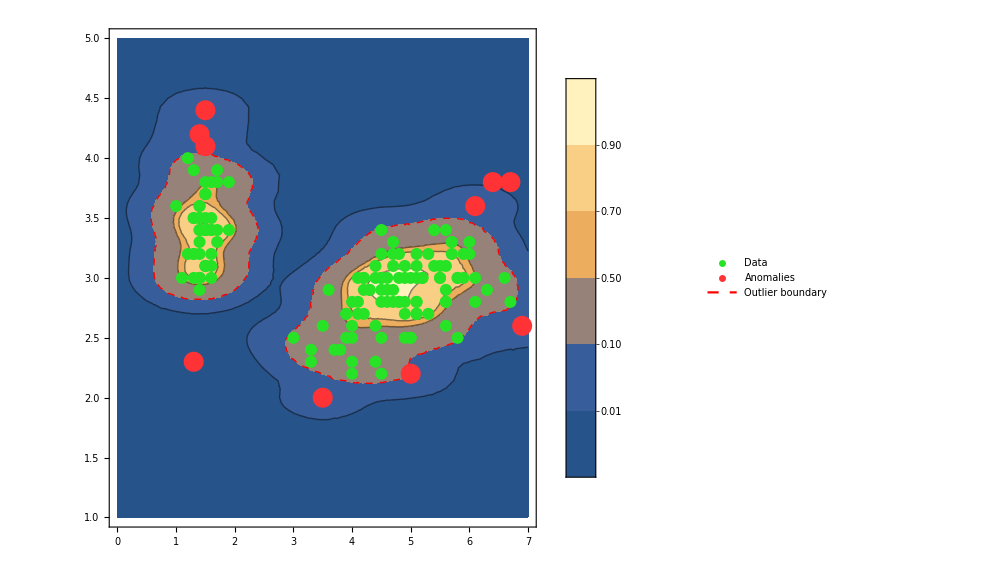

```mathematica
outliers=FindAnomalies[ad,data,AcceptanceThreshold->0.1];
Legended[Show[ContourPlot[ad[{x,y}*Quantity[1,"Centimeters"],"RarerProbability"],{x,0,7},{y,1,5},PlotRange->All,Contours->{0.9,0.7,0.5,{0.1,Directive[Thickness[Large],Dashing[{Small,Small}],RGBColor[1,0,0]]},0.01},PlotLegends->Automatic,ImageSize->200],ListPlot[{data,outliers},],ImageSize-> Large],LineLegend[{Directive[Thick,Dashed,Red]},{"Outlier boundary"}]]
```

## DeleteAnomalies

Obtain a dataset of images:

```mathematica
train=RandomSample[ResourceData["MNIST","TrainingData"]⟦All,1⟧,30000];
```

```mathematica
RandomSample[train,10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Train an anomaly detector on the training set:

```mathematica
ad=AnomalyDetection[train,Method->"Multinormal"]
```

AnomalyDetectorFunction[…]

Test data:

```mathematica
data={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

Remove anomalous examples from the test dataset:

```mathematica
DeleteAnomalies[ad,data]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Stage 5: Communicate

## Visualizations

This notebook provides examples of code to create visualizations that are helpful in communicating the message at the end of a multiparadigm data science project.

### A Simple Visualization for a Single Feature

Get the population of the countries in the G7:

```mathematica
data =EntityClass["Country","GroupOf7"][EntityProperty["Country","Population"],"EntityAssociation"]
```

<|Canada→36624199 people,France→64979548 people,Germany→82114224 people,Italy→59359900 people,Japan→127484450 people,United Kingdom→66181585 people,United States→324459463 people|>

Visualize the data in a BarChart:

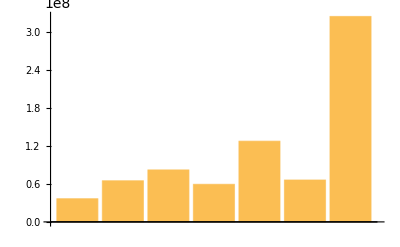

```mathematica
BarChart[data]
```

Add ChartLabels to identify the countries:

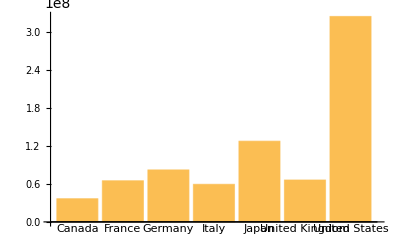

```mathematica
BarChart[data,
ChartLabels->Keys@data]
```

Place the labels above the bars instead of crowding the x axis:

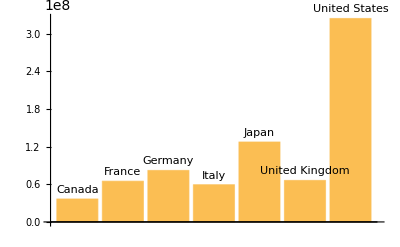

```mathematica
BarChart[data,
ChartLabels->Placed[Keys@data,Above]]
```

Place each label in a Callout:

```mathematica
BarChart[data,
ChartLabels->Callout[Keys@data,Above]]
```

-Graphics-

Add AxesLabel:

```mathematica
BarChart[data,
ChartLabels->Callout[Keys@data,Above],
AxesLabel->{None,"Population"}]
```

-Graphics-

Add AxesLabel:

```mathematica
BarChart[data,
ChartLabels->Callout[Keys@data,Above],
Frame-> True,
FrameLabel->{None,"Population"}]
```

-Graphics-

Use FrameLabel to label the axes and add a caption using PlotLabel:

```mathematica
BarChart[data,
ChartLabels->Callout[Keys@data,Above],
Frame-> {True,True,False,False},
FrameLabel->{None,"Population"},
PlotLabel->"Population of G7 Countries"]
```

-Graphics-

Add some style and colors using PlotTheme and ChartStyle:

```mathematica
BarChart[data,
ChartLabels->Callout[Keys@data,Above],
Frame-> {True,True,False,False},
FrameLabel->{None,"Population"},
PlotLabel->"Population of G7 Countries",
PlotTheme->"Business",
ChartStyle->"DarkRainbow"]
```

-Graphics-

Create a full-sized image by setting ImageSize and set the size of the text to match the large size of the image using BaseStyle:

```mathematica
BarChart[data,
ChartLabels->Callout[Keys@data,Above],
Frame-> {True,True,False,False},
FrameLabel->{None,"Population"},
PlotLabel->"Population of G7 Countries",
PlotTheme->"Business",
ChartStyle->"DarkRainbow",
ImageSize->Large,
BaseStyle->Directive[FontFamily->"Helvetica",FontSize->18]]
```

-Graphics-

### Visualizing Two Features for Every Sample

Get the population and GDP per capita for each country in the G7:

```mathematica
data2 = EntityClass["Country","GroupOf7"][{EntityProperty["Country","Population"],},"EntityAssociation"]
```

<|Canada→{36624199 people,45032.1 $},France→{64979548 people,38476.7 $},Germany→{82114224 people,44469.9 $},Italy→{59359900 people,31953. $},Japan→{127484450 people,38428.1 $},United Kingdom→{66181585 people,39720.4 $},United States→{324459463 people,59531.7 $}|>

Visualize the data in a RectangleChart:

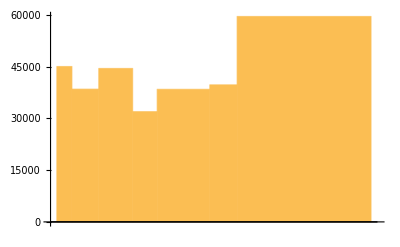

```mathematica
RectangleChart[data2]
```

Annotate the chart and add styling options:

```mathematica
RectangleChart[data2,
ChartLabels->Callout[Keys@data],
FrameLabel->{"Population","GDPPerCapita"},
LabelStyle->14,
PlotLabel->"Population of G7 Countries",
PlotTheme->"Business",
ImageSize->450,
ChartStyle->"DarkRainbow"]
```

-Graphics-

### Visualizing Three Features for Every Sample

Get the population, GDP per capita and life expectancy for each country in the G7:

```mathematica
data3 =  EntityClass["Country","GroupOf7"][{EntityProperty["Country", "GDP", {"CurrencyUnit" -> "CurrentUSDollar", 
   "PerCapita" -> "PerCapita"}],
"LifeExpectancy",
"Population"},
"EntityAssociation"]
```

<|Canada→{45032.1 $,82.3005 yr,36624199 people},France→{38476.7 $,82.2732 yr,64979548 people},Germany→{44469.9 $,80.6415 yr,82114224 people},Italy→{31953. $,82.5439 yr,59359900 people},Japan→{38428.1 $,83.9849 yr,127484450 people},United Kingdom→{39720.4 $,80.9561 yr,66181585 people},United States→{59531.7 $,78.6902 yr,324459463 people}|>

Visualize the data in a BubbleChart:

```mathematica
BubbleChart[
Values@data3,
ChartLabels->Callout[Keys@data3],
FrameLabel->{"GDPPerCapita","LifeExpectancy"},
PlotTheme->"Detailed",
ChartStyle->"IslandColors",ChartLegends->BarLegend[{"IslandColors",QuantityMagnitude[MinMax[data3[[All,3]]]]}]]
```

-Graphics-

Write a function to create a Grid of information to present as a Tooltip for each data point in the chart:

```mathematica
makeToolTip[c_]:= 
Grid[
Join[
{{Style[c["Name"],"Text",Bold,18],SpanFromLeft}},
Transpose[{{"LifeExpectancy","GDPPerCapita","Population"},
c[{"LifeExpectancy",EntityProperty["Country", "GDP", {"CurrencyUnit" -> "CurrentUSDollar", 
   "PerCapita" -> "PerCapita"}],"Population"}]}]
],
Alignment->Left,
Frame->All,
Background->{None,{LightGray,None}}]
```

```mathematica
makeToolTip[Entity["Country","UnitedStates"]]
```

United States | 
LifeExpectancy | 78.6902 yr
GDPPerCapita | 59531.7 $
Population | 324459463 people

Add the custom tooltip to the chart and also add a legend to interpret the colors for the bubbles:

```mathematica
BubbleChart[
MapThread[Callout,{Values@data3,Keys@data3}],
ChartLabels->Placed[makeToolTip[#]&/@Keys@data3,Tooltip],
FrameLabel->{"GDPPerCapita","LifeExpectancy"},
PlotTheme->"Detailed",
ChartStyle->"IslandColors",ChartLegends->BarLegend[{"IslandColors",QuantityMagnitude[MinMax[data3[[All,3]]]]}]]
```

-Graphics-

### Making It Interactive

Visualizations can be made more engaging by adding interactivity:

Use Manipulate to select from the list of continents and look at the countries in that continent:

```mathematica
Manipulate[
EntityValue[continent,"Name"],{{continent,EntityClass["Country","Asia"],Style["Continent:","Text",14]},
{EntityClass["Country","Asia"]-> "Asia",EntityClass["Country","Europe"]-> "Europe",EntityClass["Country","Africa"]-> "Africa",EntityClass["Country","NorthAmerica"]-> "NorthAmerica",EntityClass["Country","SouthAmerica"]-> "SouthAmerica",EntityClass["Country","Oceania"]-> "Oceania"}
}]
```

Replace the "Name" with code to access "GDP",  "LifeExpectancy" and "Population" for each country and create the BubbleChart for each continent:

```mathematica
Manipulate[With[{data=EntityValue[continent,{EntityProperty["Country", "GDP", {"CurrencyUnit" -> "CurrentUSDollar", 
   "PerCapita" -> "PerCapita"}],"LifeExpectancy","Population"},"EntityAssociation"]},
BubbleChart[
Values@data,
ChartLabels->Placed[makeToolTip[#]&/@Keys@data,Tooltip],
FrameLabel->{"GDPPerCapita","LifeExpectancy"},
PlotTheme->"Detailed",
ChartStyle->"IslandColors",ChartLegends->BarLegend[{"IslandColors",QuantityMagnitude[MinMax[data[[All,3]]]]}]]],{{continent,EntityClass["Country","Asia"],Style["Continent:","Text",14]},{EntityClass["Country","Asia"]-> "Asia",EntityClass["Country","Europe"]-> "Europe",EntityClass["Country","Africa"]-> "Africa",EntityClass["Country","NorthAmerica"]-> "NorthAmerica",EntityClass["Country","SouthAmerica"]-> "SouthAmerica",EntityClass["Country","Oceania"]-> "Oceania"}}]
```

data$::shdw: Symbol data$ appears in multiple contexts {DataCleaning`,Global`}; definitions in context DataCleaning` may shadow or be shadowed by other definitions.

#### Mind the axes scale: recreating the GapMinder World Health-Wealth Chart

The bubble charts are based on the visualizations made popular by Hans Rosling at gapminder.org, specifically the World Health Chart.

The chart on the video looks different from the chart created by directly plotting life expectancy against GDP per capita.

Download the data for GDP per capita, life expectancy and population for all the member countries of the United Nations:

```mathematica
data =DeleteMissing[
EntityValue[
EntityClass["Country","UnitedNations"],EntityFunction[e,{e[ "GDP", {"CurrencyUnit" -> "CurrentUSDollar", 
   "PerCapita" -> "PerCapita"}],e["LifeExpectancy"],e["Population"]}],
"EntityAssociation"],
1,Infinity];
```

Create the BubbleChart:

```mathematica
BubbleChart[
Values@data,
ChartLabels->Callout[Keys@data],
ImageSize->450,
LabelStyle->14,
FrameLabel->{"Income Per Person","Life Expectancy"},
PlotTheme->"Detailed",
ChartStyle->"DarkRainbow"]
```

-Graphics-

Restrict PlotRange to leave out countries with GDP per capita more than 100,000:

```mathematica
BubbleChart[
data,
ChartLabels->Callout[Keys@data],
ImageSize->450,
LabelStyle->14,
FrameLabel->{"Income Per Person","Life Expectancy"},
PlotTheme->"Detailed",
ColorFunction->(ColorData["DarkRainbow"][# #2]&),
PlotRange->{{500,100000},Automatic}]
```

-Graphics-

Use log of GDP per capita instead:

```mathematica
dataLogGDP =DeleteMissing[EntityValue[EntityClass["Country","UnitedNations"],EntityFunction[e,{N@Log10@QuantityMagnitude@e[ "GDP", {"CurrencyUnit" -> "CurrentUSDollar", 
   "PerCapita" -> "PerCapita"}],e["LifeExpectancy"],e["Population"]}],"EntityAssociation"],1,Infinity];
```

Recreate the chart with the GDP per capita on the x axis in log scale:

```mathematica
BubbleChart[
dataLogGDP,
ChartLabels->Callout[Keys@dataLogGDP],
ImageSize->450,
LabelStyle->14,
FrameLabel->{"Income Per Person","Life Expectancy"},
PlotTheme->"Detailed",ColorFunction->(ColorData["IslandColors"][# #2]&),
FrameTicks->{{Automatic, None},{{#,10^#}&/@Range[5],None}},
AspectRatio->2/3]
```

-Graphics-

### Visualization Examples

#### Visualization examples: energy production by countries in the G7

Download data for electricity production by each of the G7 countries:

```mathematica
data = EntityValue[EntityClass["Country","GroupOf7"], {"ElectricityWind", "ElectricityNuclear",
     "ElectricityHydroelectric", "ElectricityBiomass", 
    "ElectricityConventionalThermal"}];
```

Create a labeled bar chart to communicate the information:

```mathematica
BarChart[data,ChartLabels->{Callout[{"Canada","France","Germany","Italy","Japan","United Kingdom","United States"},LabelStyle->16],None},Sequence[ChartStyle->58,PlotTheme->"Web",ImageSize->450,ChartBaseStyle->EdgeForm[RGBColor[1,1,1,1]],BarSpacing->{0,2},LabelStyle->12,ScalingFunctions->"Log",ChartLegends->Placed[{"Wind","Nuclear","Hydroelectric","Biomass","ConventionalThermal"},Below],FrameLabel->Automatic]]
```

-Graphics-

#### Visualization examples: largest petroleum-producing countries

Obtain the petroleum production by total number of barrels for each country:

```mathematica
data=DeleteMissing[EntityValue[EntityClass["Country","Countries"],{"Entity",EntityProperty["Country","PetroleumTotalBarrels",{"ResourceTransaction"->"Production"}]}],1,Infinity];
```

Select those whose production is above the top 10%:

```mathematica
top10=Quantile[data[[All,2]],0.9]
```

945128. bbl oil/day

```mathematica
oildata=Select[data,#[[2]]>top10&];
```

Create a GeoBubbleChart to show the countries producing more than a million barrels:

```mathematica
GeoBubbleChart[Rule@@@oildata,LabelingFunction->(If[#[[3]]>10^6,Callout[oildata[[Last@#2,1]]],None]&),ColorFunction->"Rainbow",ImageSize->550,PlotTheme->"Marketing",LabelStyle->14,GeoGridLines->None]
```

-Graphics-

#### Visualization examples: earthquakes in 2019

List the earthquakes around the world along with properties like "Position", "Magnitude", "Period", etc. since the beginning of 2019:

```mathematica
earthquakes =EarthquakeData[All,4,{{2019,1,1},Today}];
```

Plot a density histogram of the geographic locations according to the number of earthquakes at the location:

```mathematica
GeoHistogram[Values[#["Position"]& /@ earthquakes],50,
PlotLegends->Automatic,
PlotLabel->"Number of earthquakes around the world",
ImageSize->Large]
```

-Graphics-

Plot a density histogram of the geographic locations according to the number of earthquakes at the location:

```mathematica
GeoRegionValuePlot[Values[{#["Position"], Round@#["Magnitude"]}& /@ earthquakes],
PlotLegends->Automatic,
PlotLabel->"Magnitude of earthquakes at locations",
ImageSize->Large,
GeoLabels->(Tooltip[#1,#4]&) ]
```

-Graphics-

#### Visualization examples: wind direction at University of Illinois—Willard Airport (2019)

Obtain the "WindDirection" from the WeatherData for weather station “KCMI” at University of Illinois—Willard Airport since the beginning of 2019:

```mathematica
windData=WeatherData["KCMI","WindDirection",{{2019,1,1},Today}];
```

Write code to extract the widths and heights of the bars from a Histogram:

```mathematica
sowingBar[{{x0_,x1_},{y0_,y1_}},__]:=
(Sow[{x1-x0,100*(y1-y0)}];Rectangle[{x0,y0},{x1,y1}])
```

Extract the information for each 10 degrees of the 360 degrees of direction from the Histogram:

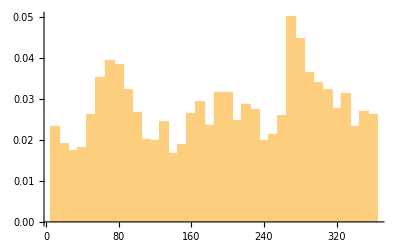
{-Graphics-,{{{10.,2.33485},{10.,1.90774},{10.,1.7369},{10.,1.82232},{10.,2.61959},{10.,3.53075},{10.,3.92938},{10.,3.84396},{10.,3.21754},{10.,2.67654},{10.,2.02164},{10.,1.99317},{10.,2.44875},{10.,1.67995},{10.,1.87927},{10.,2.64806},{10.,2.9328},{10.,2.36333},{10.,3.16059},{10.,3.16059},{10.,2.47722},{10.,2.87585},{10.,2.73349},{10.,1.99317},{10.,2.13554},{10.,2.59112},{10.,5.01139},{10.,4.47039},{10.,3.64465},{10.,3.38838},{10.,3.21754},{10.,2.76196},{10.,3.13212},{10.,2.33485},{10.,2.70501},{10.,2.61959}}}}

```mathematica
{histogram,newdata}=Reap[Histogram[windData,Automatic,"Probability",ChartElementFunction->sowingBar]]
```

Use the information from the Histogram to plot the "WindDirection" data on a SectorChart:

```mathematica
SectorChart[newdata,
SectorOrigin->{Pi/2,"Clockwise"},
PolarAxes->True,
PolarGridLines->Automatic,
PolarTicks->{"Direction",Automatic},
ChartBaseStyle->Directive[Opacity[1],EdgeForm[Thin]],
LabelingFunction->(Placed[#[[2]],Tooltip]&)]
```

-Graphics-

#### Visualization examples: graphs from words and texts

Find words in the English dictionary that start with the letters w-o-l-f:

```mathematica
words=DictionaryLookup["wolf*"]
```

{wolf,wolfed,wolfhound,wolfhounds,wolfing,wolfish,wolfishly,wolfram,wolfs}

Find the three nearest words to each of the words in the preceding list:

```mathematica
nearbys=Flatten[Map[(Thread[#->DeleteCases[Nearest[words,#,3],#]])&,words]]
```

{wolf→wolfs,wolf→wolfed,wolfed→wolf,wolfed→wolfs,wolfhound→wolfhounds,wolfhound→wolfed,wolfhounds→wolfhound,wolfhounds→wolfed,wolfing→wolfish,wolfing→wolf,wolfish→wolfing,wolfish→wolfishly,wolfishly→wolfish,wolfishly→wolfing,wolfram→wolf,wolfram→wolfed,wolfs→wolf,wolfs→wolfed}

Draw a graph with edges between the nearest words:

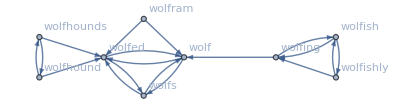

```mathematica
Graph[nearbys,VertexLabels->Automatic]
```

Find the 10 nearest words in the dictionary to the word “wolf” and draw the NearestNeighborGraph for them:

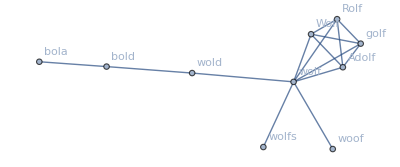

```mathematica
NearestNeighborGraph[Nearest[DictionaryLookup[]]["wolf",10],VertexLabels->Automatic]
```

Draw a graph to show how letters in a word occur one after the other:

```mathematica
wordPlot[w_String]:=Graph[(x=Characters[w];
Thread[Drop[x,-1]->Drop[x,1]]),VertexLabels->Automatic,DirectedEdges->True];
```

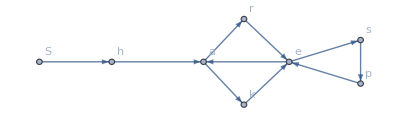

```mathematica
wordPlot["Shakespeare"]
```

Draw a graph to show how words in a sentence are linked to subsequent words:

```mathematica
textPlot[w_String]:=GraphPlot[(x=Map[ToLowerCase,StringCases[w,WordCharacter..]];
g=Thread[Drop[x,-1]->Drop[x,1]];
g),DirectedEdges->True,VertexLabels->Automatic];
```

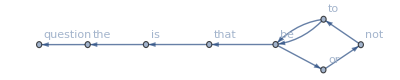

```mathematica
textPlot["to be or not to be, that is the question."]
```

## Automated Reports

The following examples demonstrate the use of some basic commands to script and generate a report.

### Create a Notebook Programmatically

Generate a simple report in a notebook with the CreateDocument function:

```mathematica
CreateDocument[
{"This is a report",
DateListPlot[RandomReal[2,100],{2017,03,1}]
}]
```

e76pe_shm104FrontEndObject[LinkObject["e76pe_shm", 3, 1]]104Untitled-1

Add formatting elements to the report notebook:

```mathematica
CreateDocument[
{TextCell["This is a report","Section"],
ExpressionCell[DateListPlot[RandomReal[2,100],{2017,03,1}]]
}]
```

e76pe_shm105FrontEndObject[LinkObject["e76pe_shm", 3, 1]]105Untitled-2

Obtain a list of countries in the South Asian Association for Regional Cooperation:

```mathematica
EntityList[EntityClass["Country","SouthAsianAssociationForRegionalCooperation"]]
```

{Afghanistan,Bangladesh,Bhutan,India,Maldives,Nepal,Pakistan,Sri Lanka}

Write code to generate a report, with individual sections for each of the countries containing similar information about their population:

```mathematica
CreateDocument[
CellGroup[{
TextCell[#,"Section"],
TextCell["Top 10 Populated Cities","Subsection"],
ExpressionCell[
GeoBubbleChart[EntityValue[EntityClass["City",{EntityProperty["City","Country"]->#,EntityProperty["City","Population"]->TakeLargest[10]}],"Population","EntityAssociation"],ChartLabels->Callout[EntityList[EntityClass["City",{EntityProperty["City","Country"]->#,EntityProperty["City","Population"]->TakeLargest[10]}]]]],"Output"],
TextCell["Population Since 1900","Subsection"],
ExpressionCell[
DateListPlot[
#[],PlotLabel->"Population Since 1900"]
,"Output"]
},
Closed]&
/@EntityList[EntityClass["Country","SouthAsianAssociationForRegionalCooperation"]],
WindowTitle->"SAARC Countries",
StyleDefinitions->"Report/AutomatedReport.nb"]
```

syt3e_shm76FrontEndObject[LinkObject["syt3e_shm", 3, 1]]76SAARC Countries

### Report Generation from Templates

Template notebooks provide a way to automate customized generation of reports.

The menu File ▶ New ▶ Programmatic Notebook ▶ Template Notebook can be used to create a template notebook. Alternatively, template notebooks can be created using CreateNotebook.

Create a new template notebook:

```mathematica
templateNo=CreateNotebook["Template"]
```

e76pe_shm108FrontEndObject[LinkObject["e76pe_shm", 3, 1]]108Untitled-3

The buttons in the template toolbar can be used to control the placement and behavior of template variables (“slots” and “expressions”).

Insert a “slot” for name of a “country”. Provide a default value (do not forget quotes around the country name).

Insert an “expression” for CurrentDate[“Year”].

Style the cell as “Section”.

Add code to a new cell (Input) to plot the “GDP” and “NationalIncome” of a country for the last 20 years.

Example:

to = CurrentDate[“Year”];
from = DatePlus[to,-Quantity[20,”Years”]];
gdp = CountryData[“Argentina”,{{“GDP”},{from[“Year”],to[“Year”]}}][“DatePath”];
nationalIncome =CountryData[“Argentina”,{{“NationalIncome”},{from[“Year”],to[“Year”]}}][“DatePath”];
DateListPlot[Map[Tooltip[#,#[[1]][“Year”]]&,{gdp,nationalIncome},{2}],PlotMarkers→Automatic,PlotLabel→ "Argentina",PlotLegends→{“GDP”,”NationalIncome”}]

Set “CellBehavior” to “Evaluate and Hide”.

Set a stylesheet for the report using menu option Format ▶ Stylesheet ▶ Report ▶ StandardReport.

Save the template notebook.

Preview a copy of the report. Generate a document from the template. This uses the default slot values.

Open an existing template notebook:

```mathematica
myreportTemplate=NotebookOpen[FileNameJoin[{NotebookDirectory[],"Resources","TemplateExample.nb"}]]
```

e76pe_shm112FrontEndObject[LinkObject["e76pe_shm", 3, 1]]112TemplateExample.nb/Users/abritac/Documents/Training/EIDS/DataScienceWRIInternalClass/data/TemplateExample.nb

Generate a document from the template, providing specific values for the “slots” in the template:

```mathematica
report=GenerateDocument[myreportTemplate,<|"country"->"Chile"|>]
```

e76pe_shm114FrontEndObject[LinkObject["e76pe_shm", 3, 1]]114Untitled-5

Close the template and generated report notebook:

```mathematica
NotebookClose/@{myreportTemplate,report};
```

Repeating blocks can be used in a template to loop over a list of supplied slot values.

Open an existing template notebook with examples of repeating blocks:

```mathematica
myreportTemplateRepeating=NotebookOpen[FileNameJoin[{NotebookDirectory[],"Resources","TemplateRepeatingBlockExample.nb"}]]
```

e76pe_shm115FrontEndObject[LinkObject["e76pe_shm", 3, 1]]115TemplateRepeatingBlockExample.nb/Users/abritac/Documents/Training/EIDS/DataScienceWRIInternalClass/data/TemplateRepeatingBlockExample.nb

Generate a document from the template,  where the repeating blocks loop over the countries in a continent:

```mathematica
whichContinent = "SouthAmerica";
```

```mathematica
reportRepeating=GenerateDocument[myreportTemplateRepeating,<|"continent"-> whichContinent,"countries"->Map[<|"country"->#|>&,CountryData[whichContinent]]|>]
```

e76pe_shm117FrontEndObject[LinkObject["e76pe_shm", 3, 1]]117Untitled-6

Close the template and generated report notebook:

```mathematica
NotebookClose/@{myreportTemplateRepeating,reportRepeating};
```

### Automated Report Generation

Document generators can be deployed to the cloud with driver code to compute the values needed to fill in report templates. The following examples demonstrate the use of a generator that produces a daily report on the performance over the past seven days of the three stocks with the highest trading volumes on the previous day, from a specific industry sector.

List the industry sectors to choose from:

```mathematica
FinancialData["Sectors"]
```

Choose a sector randomly:

```mathematica
RandomChoice[FinancialData["Sectors"]]
```

Or set a specific sector and metric of performance:

```mathematica
sector="PersonalComputers";
metric="Volume";
```

Write the driver code that will automatically obtain the information for the report:

```mathematica
Clear[driver];
driver[mDays_Integer, nStocks_Integer]:=Block[{members,reportOn},
members=FinancialData[sector,"Members"];
reportOn=Take[Reverse[SortBy[
({#,Quiet[FinancialData[#,metric,{Yesterday}]]}&/@members)/.{{_,_Missing|_FinancialData}->Sequence[],{t_String,{{_List,i_Integer}}}:>{t,i}},
Last
]],nStocks][[All,1]];
<|
"Start":>DateString[DatePlus[Today,-mDays],"DateShort"],
"Stocks"->(
<|"Name"->FinancialData[#,"Company"],"Ticker"->#|>&/@reportOn)
|>
]&;
```

Deploy a DocumentGenerator to the cloud along with the driver code to trigger automatic report generation:

```mathematica
With[{dest="My-reports/"<>sector},
Quiet@DeleteDirectory[CloudObject[dest],DeleteContents->True];
co=CloudDeploy[DocumentGenerator[
File["ExampleData/StocksTemplate.nb"],
driver[7,3],
DateObject[{_,_,Tuesday|Wednesday|Thursday|Friday|Saturday,1}],
DeliveryFunction->"PDF"
],dest]
]
```

The generation time for this report is potentially long, so this is an example of a case where asynchronous evaluation is preferable.

Trigger the generator to run asynchronously:

```mathematica
TaskExecute[co]
```

Remove the generator to stop the automated report generation:

```mathematica
TaskRemove[co];
```

### References

The following Wolfram Language™ workflows show how to:

Create a notebook programmatically

Generate a report from a template

Generate a report as a PDF

Generate a report according to a schedule

A collection of report generating functionality can be viewed at Automated Reports.

## Microsites and Web Apps

### CloudPublish

The easiest way to share a notebook is to use CloudPublish.

Create a simple notebook:

```mathematica
nb=Notebook[{Cell["head","Section"],Cell["text","Text"]}];
```

Make a public copy of the notebook in the cloud, using CloudPublish:

```mathematica
CloudPublish[nb]
```

CloudObject[https://www.wolframcloud.com/objects/72ca0fd3-2eeb-40e8-815a-19a62baebd00]

### CloudDeploy

CloudDeploy can be used to deploy Wolfram Language™ expressions, as simple as a piece of text or as complex as a web app, to the cloud.

Deploy some stylized text to the cloud:

```mathematica
CloudDeploy[Style["Hello World","72",Darker[Red]]]
```

Create an interactive visualization of the population of countries by continent and deploy it to the cloud:

```mathematica
data =EntityValue[#,"Population","EntityAssociation"] &/@ EntityValue[EntityClass["GeographicRegion","Continents"],"Countries","EntityAssociation"];
```

```mathematica
populations =Manipulate[GeoRegionValuePlot[data[Entity["GeographicRegion",continent]]],{{continent,"Asia"},{"Africa","Asia","Australia","Europe","NorthAmerica","SouthAmerica"}},SaveDefinitions->True]
```

```mathematica
CloudDeploy[populations,CloudObject["ContinentPopulationManipulate"],Permissions->"Public"]
```

Create a report on the stock prices of Amazon, Apple, IBM and Microsoft since the beginning of 2019 using a template notebook and deploy it to the cloud:

```mathematica
stocksNB = GenerateDocument["ExampleData/StocksTemplate.nb",<|"Start"->"1 Jan 2019","Stocks"->{<|"Name"->"Amazon","Ticker"->"AMZN"|>,<|"Name"->"Apple","Ticker"->"AAPL"|>,<|"Name"->"IBM","Ticker"->"IBM"|>,<|"Name"->"Microsoft","Ticker"->"MSFT"|>}|>];
```

```mathematica
CloudDeploy[stocksNB,CloudObject["StockReport"],Permissions->"Public"]
```

### EmbedCode

To add computational results to an existing webpage, Wolfram Language objects can be deployed to the cloud and then embedded on a webpage. EmbedCode generates the code necessary to embed the object.

Create a timeline plot of the notable artworks of Claude Monet:

```mathematica
With[{data =DeleteMissing[EntityValue[EntityValue[Entity["Person","ClaudeMonet::9qbxq"],EntityProperty["Person","NotableArtworks"]],{"CompletionDate","StartDate","Image","Name","Area"}],1,1]},
TimelinePlot[Interval[{#[[1]],#[[2]]}]->Tooltip[#[[3]],#[[4]]]&/@data[[All,1;;4]],PlotLabel->"A Timeline of Monet's Artworks"]]
```

-Graphics-

Deploy the timeline to the cloud and generate code that can be used to embed it in a webpage:

```mathematica
EmbedCode[CloudDeploy[picture,CloudObject["monetTimeline"], Permissions->"Public"]]
```

Embeddable Code
Use the code below to call the Wolfram Cloud function from HTML:
Code
 | Copy to Clipboard
<iframe src="https://www.wolframcloud.com/objects/online-courses/DataScienceMOOC/Examples/monetTimeline?_embed=iframe" width="600" height="800"></iframe>

### FormFunction

FormFunction can be used to create a web form that can accept some input, process it and return an output.

FormFunction has three main parts:

FormObject: the HTML form (input fields and their specifications)

A pure function: specifies what to do with the input

A return type (optional): how the result of part 2 is returned

Create a FormObject that accepts a string input and returns a concatenated string as output:

```mathematica
FormFunction[FormObject[<|"name"->"String"|>],"hello "~~#name&,"PNG"]
```

FormFunction[]

Create and deploy a simple form that accepts only one string input, uses a pure function to append it to the string “may the force be with you...”, adds the image of Yoda and and returns the result as a PNG image:

```mathematica
CloudDeploy[FormFunction[FormObject[<|"name"->"String"|>],Labeled[Entity["FictionalCharacter","Yoda"]["Image"],"May the force be with you "~~#name,Right]&,"PNG"],CloudObject["SimpleFormExample"]]
```

Create an Instagram-like image-filtering app that accepts as input an image and a choice of filter, then applies the filter to the image and returns the result:

```mathematica
formGram = 
FormPage[
{"image" ->"Image", 
"filter" -> ImageEffect[]}, 
ImageEffect[#image, #filter]&,
AppearanceRules-> {"Title" -> "Wolf(g)ram"}
];
CloudDeploy[formGram,CloudObject["AdvancedFormExample"]]
```

### References

There is more about the functionality for generating forms and webpages on this guide page on Creating Forms and Apps.

The tutorial Advanced Web Form Creation provides additional resources for the creation of more advanced web forms.

## Updated by Vlad Dobrin - University of Maryland MATH299M/CMSC389W Fall 2018 August 14, 2020